Use ellipses for level curves - they are easy to read.
Use something more complex for the constraint
You need to rotate them in space.

{0.707107,1.41421,2.12132,2.82843}

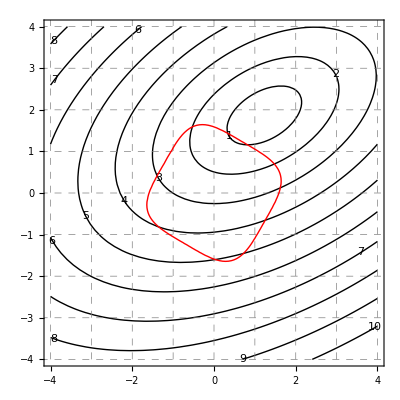

```mathematica
Table[n*Sqrt[2]/2.,{n,1,4}]
F[x_,y_]=Sqrt[(x-2)^2+3(y-1)^2];
G[x_,y_]=x^4+y^4;
rotateX[theta_]={Cos[theta],Sin[theta]};
rotateY[theta_]={-Sin[theta],Cos[theta]};
fAngle=Pi/6;
gAngle=Pi/3;
levelCurves=ContourPlot[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,{x,-4,4},{y,-4,4},
Contours->10,
ContourStyle->{Thick},
ContourLabels->(Text[#3,{#1,#2},Background->White]&),
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
GridLinesStyle->Directive[Gray,Dashed],
ContourShading->False];
constraint=ContourPlot[G[{x,y}.rotateX[gAngle],{x,y}.rotateY[gAngle]]==4,{x,-4,4},{y,-4,4},
ContourStyle->{Red,Thick}];
Show[levelCurves,constraint]
```

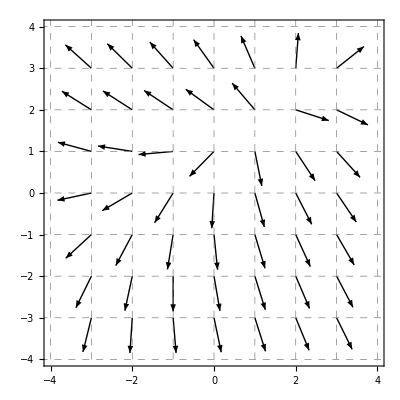

```mathematica
F[x_,y_]=Sqrt[(x-2)^2+3(y-1)^2];
rotateX[theta_]={Cos[theta],Sin[theta]};
rotateY[theta_]={-Sin[theta],Cos[theta]};
fAngle=Pi/6;
gAngle=Pi/3;
grad[x_,y_]={D[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,x],D[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,y]};

gradVects=VectorPlot[grad[x,y]/Sqrt[grad[x,y].grad[x,y]],{x,-3,3},{y,-3,3},
PlotRange->{{-4,4},{-4,4}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.1,.6},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["vectors1.eps",gradVects]
```

vectors1.eps

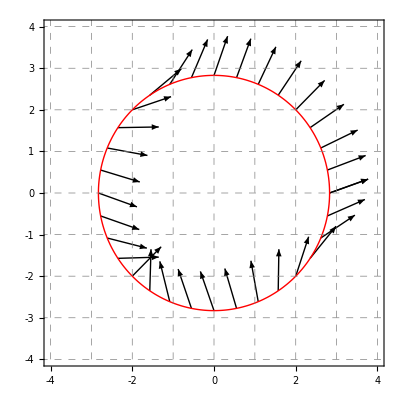

```mathematica
F[x_,y_]=Sqrt[(x-2)^2+3(y-1)^2];
F[x_,y_]=x^3+y^3+3x y;
x[t_]=Sqrt[2]2Cos[t];
y[t_]=Sqrt[2]2Sin[t];
rotateX[theta_]={Cos[theta],Sin[theta]};
rotateY[theta_]={-Sin[theta],Cos[theta]};
fAngle=0*Pi/4;
gAngle=0*Pi/4;
grad[x_,y_]={D[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,x],D[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,y]};
curve=ParametricPlot[{x[t],y[t]},{t,0,2Pi},PlotStyle->{Thick,Red}];
gradVects=Graphics[Table[Arrow[{{x[t],y[t]},{x[t],y[t]}+grad[x[t],y[t]]/Sqrt[grad[x[t],y[t]].grad[x[t],y[t]]]}],{t,0,2Pi,2Pi/32}]];
curveVector=Show[gradVects,curve,GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
GridLinesStyle->Directive[Gray,Dashed],Frame->True,FrameTicks->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},PlotRange->{{-4,4},{-4,4}}]
```

```mathematica
Solve[Sqrt[.8^2+y^2]==Sqrt[2]2,y]
```

{{y→-2.71293},{y→2.71293}}

```mathematica
Export["curveVectors1.pdf",curveVector]
```

curveVectors1.pdf

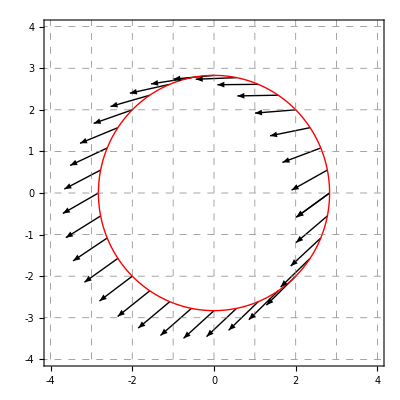

```mathematica
F[x_,y_]=(x-3)^2+3(y-4)^2;
x[t_]=Sqrt[2]2Cos[t];
y[t_]=Sqrt[2]2Sin[t];
rotateX[theta_]={Cos[theta],Sin[theta]};
rotateY[theta_]={-Sin[theta],Cos[theta]};
fAngle=-Pi/4;
gAngle=7Pi/4;
grad[x_,y_]={D[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,x],D[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,y]};
curve=ParametricPlot[{x[t],y[t]},{t,0,2Pi},PlotStyle->{Thick,Red}];
gradVects=Graphics[Table[Arrow[{{x[t],y[t]},{x[t],y[t]}+grad[x[t],y[t]]/Sqrt[grad[x[t],y[t]].grad[x[t],y[t]]]}],{t,0,2Pi,2Pi/32}]];
curveVector=Show[gradVects,curve,GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
GridLinesStyle->Directive[Gray,Dashed],Frame->True,FrameTicks->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},PlotRange->{{-4,4},{-4,4}}]
```

```mathematica
Export["curveVectors2.pdf",curveVector]
```

curveVectors2.pdf

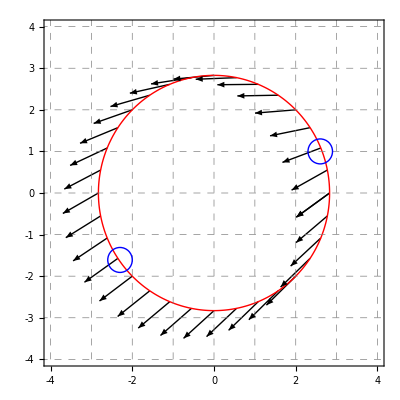

{{x→3.01802-5.02453 ⅈ,y→5.60796+2.70404 ⅈ,l→1.16539-0.493532 ⅈ},{x→3.01802+5.02453 ⅈ,y→5.60796-2.70404 ⅈ,l→1.16539+0.493532 ⅈ},{x→-2.30799,y→-1.63498,l→7.304},{x→2.63591,y→1.02566,l→-1.63478}}

```mathematica
F[x_,y_]=(x-3)^2+3(y-4)^2;
x[t_]=Sqrt[2]2Cos[t];
y[t_]=Sqrt[2]2Sin[t];
rotateX[theta_]={Cos[theta],Sin[theta]};
rotateY[theta_]={-Sin[theta],Cos[theta]};
fAngle=-Pi/4;
gAngle=7Pi/4;
grad[x_,y_]={D[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,x],D[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,y]};
curve=ParametricPlot[{x[t],y[t]},{t,0,2Pi},PlotStyle->{Thick,Red}];
gradVects=Graphics[Table[Arrow[{{x[t],y[t]},{x[t],y[t]}+grad[x[t],y[t]]/Sqrt[grad[x[t],y[t]].grad[x[t],y[t]]]}],{t,0,2Pi,2Pi/32}]];
curveVectorAns=Show[gradVects,curve,Graphics[{Thick,Blue,Circle[{2.6,1},.3],Circle[{-2.3,-1.61},.3]}],GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
GridLinesStyle->Directive[Gray,Dashed],Frame->True,FrameTicks->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},PlotRange->{{-4,4},{-4,4}}]
NSolve[{grad[x,y][[1]] ==2x l, grad[x,y][[2]]==2 y l,x^2+y^2==8} ,{x,y,l}]
```

```mathematica
Export["curveVectors2Feedback.jpg",curveVectorAns,ImageResolution->300]
```

curveVectors2Feedback.jpg

{{x→3.01802-5.02453 ⅈ,y→5.60796+2.70404 ⅈ,l→1.16539-0.493532 ⅈ},{x→3.01802+5.02453 ⅈ,y→5.60796-2.70404 ⅈ,l→1.16539+0.493532 ⅈ},{x→-2.30799,y→-1.63498,l→7.304},{x→2.63591,y→1.02566,l→-1.63478}}

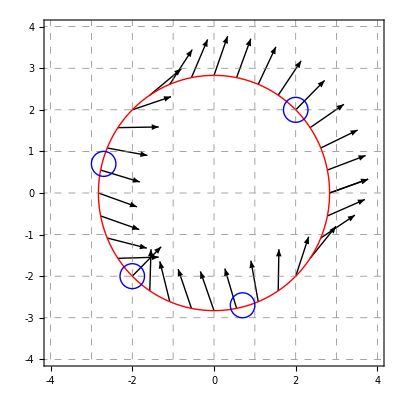

{{x→-2.73205,y→0.732051,l→-4.5},{x→2.,y→2.,l→4.5},{x→2.,y→2.,l→4.5},{x→2.,y→2.,l→4.5},{x→-2.,y→-2.,l→-1.5},{x→0.732051,y→-2.73205,l→-4.5}}

```mathematica
F[x_,y_]=Sqrt[(x-2)^2+3(y-1)^2];
F[x_,y_]=x^3+y^3+3x y;
x[t_]=Sqrt[2]2Cos[t];
y[t_]=Sqrt[2]2Sin[t];
rotateX[theta_]={Cos[theta],Sin[theta]};
rotateY[theta_]={-Sin[theta],Cos[theta]};
fAngle=0*Pi/4;
gAngle=0*Pi/4;
grad[x_,y_]={D[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,x],D[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,y]};
curve=ParametricPlot[{x[t],y[t]},{t,0,2Pi},PlotStyle->{Thick,Red}];
gradVects=Graphics[Table[Arrow[{{x[t],y[t]},{x[t],y[t]}+grad[x[t],y[t]]/Sqrt[grad[x[t],y[t]].grad[x[t],y[t]]]}],{t,0,2Pi,2Pi/32}]];
curveVectorAns=Show[gradVects,curve,Graphics[{Thick,Blue,Circle[{.7,-2.7},.3],Circle[{2,2},.3],Circle[{-2,-2},.3],,Circle[{-2.7,.7},.3]}],GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
GridLinesStyle->Directive[Gray,Dashed],Frame->True,FrameTicks->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},PlotRange->{{-4,4},{-4,4}}]
NSolve[{grad[x,y][[1]] ==2x l, grad[x,y][[2]]==2 y l,x^2+y^2==8} ,{x,y,l}]
```

```mathematica
Export["curveVectors1Feedback.jpg",curveVectorAns,ImageResolution->300]
```

curveVectors1Feedback.jpg

## Mordell Curve

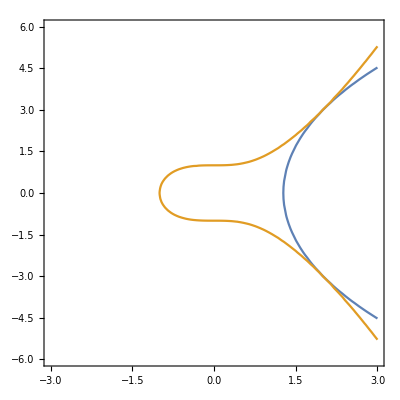

```mathematica
Clear[a,b,c,d]
g[x_,y_]=x^3+1-y^2;
gradG[x_,y_]=Grad[g[x,y],{x,y}];
f[x_,y_]=162((x-a)^2/b^2 + (y)^2/c^2 -1);
c=9;
a=14;
b=9Sqrt[2];
gradF[x_,y_]=Grad[f[x,y],{x,y}];
(*Solve[{Cross[{gradG[2,3][[1]],gradG[2,3][[2]],0}, {gradF[2,3][[1]],gradF[2,3][[2]],0}]==0,f[2,3]==0},{a,b}]*)
ContourPlot[{f[x,y]==0,g[x,y]==0},{x,-3,3},{y,-6,6}]
```

```mathematica
Solve[{gradF[x,y][[1]] == l gradG[x,y][[1]],gradF[x,y][[2]] == l gradG[x,y][[2]],x^3+1-y^2==0},{x,y,l}]
```

{{x→-7/3,y→-2/3 ⅈ √(79/3),l→-2},{x→-7/3,y→2/3 ⅈ √(79/3),l→-2},{x→-1,y→0,l→-10},{x→2,y→-3,l→-2},{x→2,y→3,l→-2},{x→(-1)^(1/3),y→0,l→2/3 (14 (-1)^(1/3)-(-1)^(2/3))},{x→-(-1)^(2/3),y→0,l→2/3 ((-1)^(1/3)-14 (-1)^(2/3))}}

```mathematica
{gradF[x,y][[1]] == l gradG[x,y][[1]],gradF[x,y][[2]] == l gradG[x,y][[2]],x^3+1-y^2==0}
```

{2 (-14+x)==3 l x^2,4 y==-2 l y,1+x^3-y^2==0}

```mathematica
g[2,3]
```

-3

```mathematica
51-34
```

17

```mathematica
Simplify[f[2,-3]]+17
```

17

```mathematica
f[2,3]
```

0

```mathematica
Solve[3x^2+x-14==0]
```

{{x→-7/3},{x→2}}

## Elliptic curve with hyperbolas

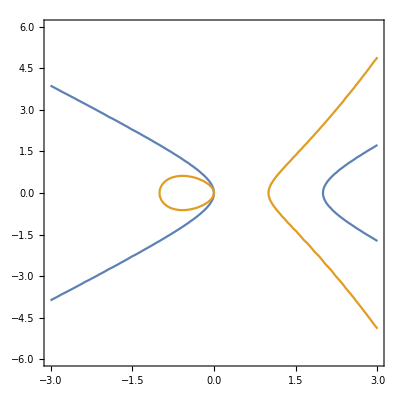

```mathematica
Clear[a,b,c,d]
g[x_,y_]=x^3-x-y^2;
gradG[x_,y_]=Grad[g[x,y],{x,y}];
f[x_,y_]=((x-a)^2/b^2 - (y)^2/c^2 -1);
c=1;
a=1;
b=1;
gradF[x_,y_]=Grad[f[x,y],{x,y}];
(*Solve[{Cross[{gradG[2,3][[1]],gradG[2,3][[2]],0}, {gradF[2,3][[1]],gradF[2,3][[2]],0}]==0,f[2,3]==0},{a,b}]*)
ContourPlot[{f[x,y]==0,g[x,y]==0},{x,-3,3},{y,-6,6}]
```

```mathematica
Solve[g[x,1]==0]
```

{{x→1/3 (27/2-(3 √69)/2)^(1/3)+(1/2 (9+√69))^(1/3)/3^(2/3)},{x→-1/6 (1+ⅈ √3) (27/2-(3 √69)/2)^(1/3)-((1-ⅈ √3) (1/2 (9+√69))^(1/3))/(2 3^(2/3))},{x→-1/6 (1-ⅈ √3) (27/2-(3 √69)/2)^(1/3)-((1+ⅈ √3) (1/2 (9+√69))^(1/3))/(2 3^(2/3))}}

```mathematica
Expand[f[x,y]]
```

-2 x+x^2-y^2